```mathematica
sx1=(Log[Rin-R0])^(1/npow)
dx1=(Log[Rout-R0]^(1/npow)-Log[Rin-R0]^(1/npow))/TS1
x1=sx1+ii*dx1
r=R0+Exp[x1^npow]
```

Log[-R0+Rin]^(1/npow)

(-Log[-R0+Rin]^(1/npow)+Log[-R0+Rout]^(1/npow))/TS1

Log[-R0+Rin]^(1/npow)+(ii (-Log[-R0+Rin]^(1/npow)+Log[-R0+Rout]^(1/npow)))/TS1

ⅇ^((Log[-R0+Rin]^(1/npow)+(ii (-Log[-R0+Rin]^(1/npow)+Log[-R0+Rout]^(1/npow)))/TS1)^npow)+R0

```mathematica
FullSimplify[r//.{ii->0},{npow>0,Rin>R0}]
FullSimplify[r//.{ii->TS1},{npow>0,Rin>R0}]
```

ⅇ^((Log[-R0+Rin]^(1/npow))^npow)+R0

ⅇ^((Log[-R0+Rout]^(1/npow))^npow)+R0

```mathematica
myRin=Solve[(Rhor==r)//.{ii->ihor},Rin]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Rin→ⅇ^(((-TS1 Log[-R0+Rhor]^(1/npow)+ihor Log[-R0+Rout]^(1/npow))/(ihor-TS1))^npow)+R0}}

```mathematica
Exp[(x^(1/n)+a)^n]
```

ⅇ^((a+x^(1/n))^n)

```mathematica
(*Clear[npow]*)
consts={npow->3,Rin->1.2,Rtorus->40,Rout->10^(10),TS1->1024,ADJUSTFACT->0.25,ihor->6+ADJUSTFACT,a->0.92 }
Rhor=1+Sqrt[1-a^2]//.consts
eq1=(Rhor==r)//.{ii->ihor}//.consts
(*eq2=(Rtorus==r)//.{ii->512}//.consts*)
(*sol=FindRoot[{eq1,eq2},{R0,-2},{npow,10},MaxIterations->1000,WorkingPrecision->100]*)
sol=FindRoot[eq1,{R0,-2},MaxIterations->1000,WorkingPrecision->100]
```

{npow→3,Rin→1.2,Rtorus→40,Rout→10000000000,TS1→1024,ADJUSTFACT→0.25,ihor→6+ADJUSTFACT,a→0.92}

1.39192

1.39192==ⅇ^((Log[1.2-R0]^(1/3)+0.00610352 (-Log[1.2-R0]^(1/3)+Log[10000000000-R0]^(1/3)))^3)+R0

FindRoot::precw: The precision of the argument function (1.39192 == ⅇ^(« 1 »^« 1 » + « 1 »)^3 + R0) is less than WorkingPrecision (100.).

{R0→-3.347266366923652007665611330237420936537105382038727491411175469980628478965762672116928629476004066}

```mathematica
god=(ⅇ^(((-TS1 Log[-R0+Rhor]^(1/npow)+ihor Log[-R0+Rout]^(1/npow))/(ihor-TS1))^npow)+R0)//.sol//.consts
```

1.2

```mathematica
r//.sol//.{ii->TS1/4}//.consts
r//.sol//.{ii->TS1/2}//.consts
```

45.4972

2860.85

```mathematica
TS1/4//.consts
```

256

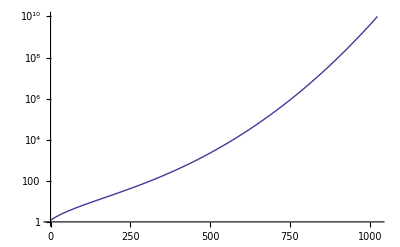

```mathematica
plotr=r//.sol//.consts;
myts1=TS1//.consts;
LogPlot[plotr,{ii,0,myts1}]
```

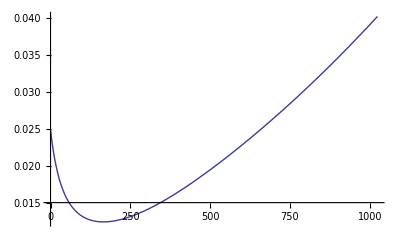

```mathematica
dror=D[plotr,ii]/plotr;
myts1=TS1//.consts;
Plot[dror,{ii,0,myts1}]
```

```mathematica
dr0=(plotr//.{ii->1})-(plotr//.{ii->0})
dt=dr0
```

0.0299483

0.0299483